### Ques. 1

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
N[E,10]
```

2.718281828

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
N[{2^(1/2),2^(1/6)},16]
```

{1.414213562373095,1.122462048309373}

### Ques. 2

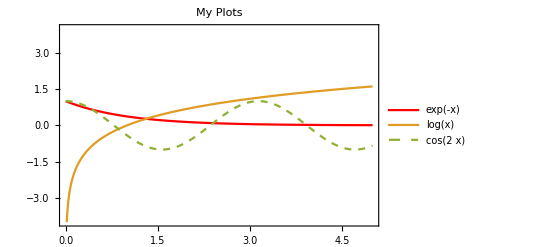

```mathematica
Plot[{Exp[-x],Log[x],Cos[2x]},{x,0,5},PlotRange->{-4,4},PlotLabel->My Plots,PlotLegends->"Expressions",PlotStyle->{Red,Thick,Dashed},Frame->True,PlotStyle->{Red,Green,Blue}]
```

### Ques. 3 (Self Doable) Ques. 4

```mathematica
Manipulate[Plot[{a x^2+b x+c,(-b^2+4 a c)/(4a)}/.a->1/.c->1,{x,-10,10},ImageSize->Large],{b,-5,5}]
```

### Ques. 5

```mathematica
Manipulate[Plot[{Log[x],x^(1/3)},{x,0,b},PlotLegends->"Expressions"],{b,1,150,0.1}]
```

```mathematica
NSolve[Log[x]-x^(1/3)==0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→6.40567},{x→93.3545}}

```mathematica
Reduce[Log[x]-x^(1/3)==0,x]//N
```

x==6.40567||x==93.3545

### Ques. 6

```mathematica
Normal[Series[Cosh[x],{x,0,2}]]
```

1+x^2/2

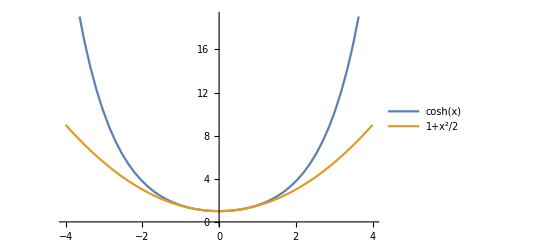

```mathematica
Plot[{Cosh[x],1+x^2/2},{x,-4,4},PlotLegends->"Expressions"]
```

```mathematica
Abs[(Normal[Series[Cosh[x],{x,0,2}]]-Cosh[x])/Cosh[x]/.x->0.5]//N
```

0.00232876

```mathematica
Abs[(Normal[Series[Cosh[x],{x,0,2}]]-Cosh[x])/Cosh[x]/.x->1]//N
```

0.0279186

### Ques. 7

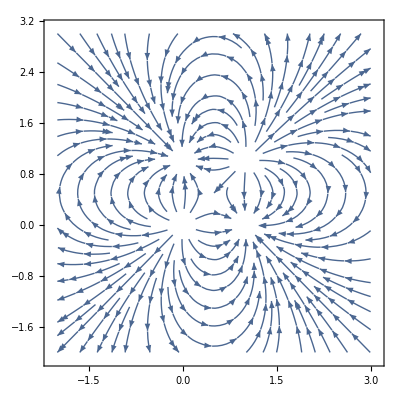

```mathematica
fieldLines=StreamPlot[{x/r^3-(x-1)/r1^3-x/r2^3+(x-1)/r3^3,y/r^3-y/r1^3-(y-1)/r2^3+(y-1)/r3^3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2) /.r2->√(x^2+(y-1)^2)/.r3->√((x-1)^2+(y-1)^2),{x,-2,3},{y,-2,3},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.05 && (x-1)^2+(y-1)^2>0.05&& (x)^2+(y-1)^2>0.05&& (x-1)^2+(y)^2>0.05]]
```

Alternatively,

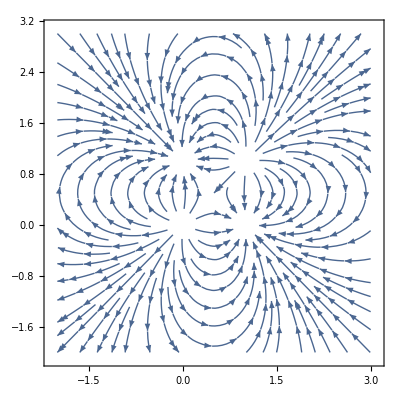

```mathematica
fieldLines=StreamPlot[{x/r^3-(x-1)/r1^3-x/r2^3+(x-1)/r3^3,y/r^3-y/r1^3-(y-1)/r2^3+(y-1)/r3^3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2) /.r2->√(x^2+(y-1)^2)/.r3->√((x-1)^2+(y-1)^2),{x,-2,3},{y,-2,3},RegionFunction->Function[{x,y,vx,vy,n},n<20]]
```

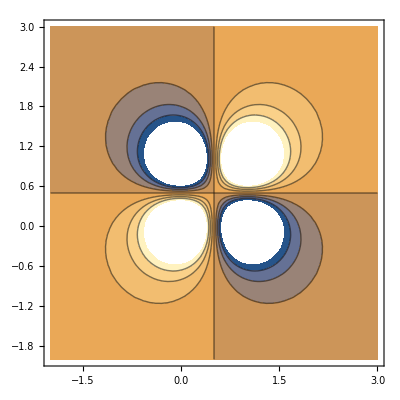

```mathematica
equiPotential=ContourPlot[{1/r-1/r1-1/r2+1/r3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2)/.r2->√(x^2+(y-1)^2)/.r3->√((x-1)^2+(y-1)^2),{x,-2,3},{y,-2,3}]
```

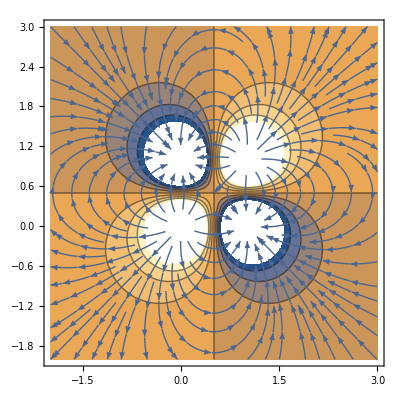

```mathematica
Show[equiPotential,fieldLines]
```

### Ques. 8

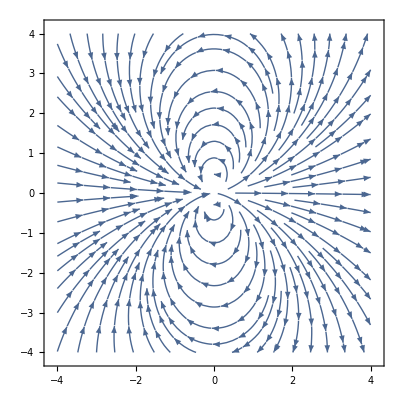

```mathematica
StreamPlot[{1/r^3(2 x^2/r^2-y^2/r^2),1/r^3(3(x y)/r^2)}/.r->√(x^2+y^2),{x,-4,4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.01]]
```